Supplemental Material: Details of STM-IETS Line Shape Simulation

On the Nature of Asymmetry in the Vibrational Line Shape of Single-Molecule
 Inelastic Electron Tunneling Spectroscopy with the STM

Chen Xu,^1 Chi-lun Chiang,^1 Zhumin Han^1 and W. Ho^(1,2,*)
^1Department of Physics and Astronomy, University of California, Irvine, California 92697-4575, USA
^2Department of Chemistry, University of California, Irvine, California 92697-2025, USA 

*To whom correspondence should be addressed: wilsonho@uci.edu

This file is also available to download at https://github.com/iets-lineshape/simulation

Refer to the original codes developed by M. Paulsson et al. for details:
M. Paulsson, T. Frederiksen, H. Ueba, N. Lorente, and M. Brandbyge, Phys. Rev. Lett. 100, 226604 (2008).

Gam1 and Gam2 are the molecule-tip and molecule-substrate couplings, respectively;
alpha = Gam2/Gam1;
e0 is the molecule resonance level;
hw is the vibrational mode energy;
M is the coupling between the tunneling electron and the vibration of molecule;
kT is the energy at temperature T. Note the model does not consider the bias modulation, so T is the effective temperature.
The new parameter “para” here is for the compensation of the offset in the asymmetric term due to the numerical integration.

I. Second derivative of current - Symmetric term

```mathematica
D2sym[alpha_,Gam1_,e0_,hw_,M_,kT_,para_,eVmev_]:=1/((4 e0^2+(1+alpha)^2 Gam1^2)^3)16 alpha Gam1^2 M^2 (-(Exp[(0.001 eVmev+hw)/kT](4 e0^2-(1+alpha)^2 Gam1^2) (0.006 Exp[(0.002 eVmev+hw)/kT]eVmev-0.006  Exp[1/kT(0.002 eVmev+3 hw)]eVmev-6 Exp[1/kT(0.001 eVmev+2 hw)]hw+6 Exp[1/kT(0.003 eVmev+2 hw)] hw+ Exp[1/kT(0.004 eVmev+3 hw)](0.001 eVmev-hw-2 kT)+ Exp[hw/kT](-0.001 eVmev+hw-2 kT)- Exp[(0.004 eVmev+hw)/kT](0.001 eVmev+hw-2 kT)+ Exp[1/kT(0.001 eVmev+4 hw)](0.001 eVmev+hw-2 kT)+ Exp[1/kT(0.003 eVmev+4hw)](0.001 eVmev-hw+2 kT)+ Exp[(0.001 eVmev)/kT](-0.001 eVmev+hw+2 kT)-Exp[(0.003 eVmev)/kT] (0.001 eVmev+hw+2 kT)+ Exp[(3 hw)/kT](0.001 eVmev+hw+2 kT)))/((-Exp[(0.001 eVmev)/kT]+Exp[hw/kT])^3 (-1+Exp[(0.001 eVmev+ hw)/kT])^3 kT^2));
```

II. Second derivative of current - Asymmetric term

```mathematica
dx=0.02; 
maxX=0.7; 
hilbM=Table[dx+(dx+x-x0) (Log[Abs[-x+x0]]-Log[Abs[-dx-x+x0]])-dx-(dx-x+x0) (Log[Abs[-x+x0]]-Log[Abs[dx-x+x0]]),{x,-maxX-.00001,maxX,dx},{x0,-maxX,maxX,dx}] 1/Pi/dx;
NN=Length[hilbM];
xx=Table[x,{x,-maxX,maxX,dx}];
nf[x_,kT_]:=1/(E^(x/kT)+1);
hTerm1[hw_,kT_]:=hTerm1[hw,kT]=hilbM.Table[nf[x+hw,kT]-nf[x-hw,kT],{x,-maxX,maxX,dx}];
hTerm2[eV_,hw_,kT_]:=hTerm2[eV,hw,kT]=Module[{},dx Apply[Plus,hTerm1[hw,kT]*Table[nf[x,kT]-nf[x-eV,kT],{x,-maxX,maxX,dx}]/2]];
dhTerm[hw_,kT_]:=Module[{tmp,tmp2},
tmp=tmp2=Table[hTerm2[V,hw,kT],{V,-maxX,maxX,dx}];
tmp2[[Range[1,Length[tmp]-1]]]=tmp[[Range[2,Length[tmp]]]];
(tmp-tmp2)/dx
];
Asym[hw_,kT_]:=Asym[hw,kT]=Interpolation[Transpose[{xx,dhTerm[hw,kT]}]];
DAsym[hw_,kT_]:=DAsym[hw,kT]=Module[{tmpx,tmp,NN=Length[xx]},
tmpx=(xx[[Range[1,NN-1]]]+xx[[Range[2,NN]]])/2;
tmp=dhTerm[hw,kT];
tmp=(tmp[[Range[2,NN]]]-tmp[[Range[1,NN-1]]])/dx;
Interpolation[Transpose[{tmpx,tmp}]]
];
D2asym[alpha_,Gam1_,e0_,hw_,M_,kT_,para_,eVmev_]:=1/((4 e0^2+(1+alpha)^2 Gam1^2)^3)16 alpha Gam1^2 M^2(-8 (-1+alpha) e0 Gam1 DAsym[hw,kT][0.001 eVmev+para]);
```

III. Second derivative of current - Complete expression

```mathematica
D2[alpha_,Gam1_,e0_,hw_,M_,kT_,para_,eVmev_]:=D2sym[alpha,Gam1,e0,hw,M,kT,para,eVmev]+D2asym[alpha,Gam1,e0,hw,M,kT,para,eVmev];
```

Case 1
Gam1 = 2, Gam2 = 0.1 (alpha = Gam2/Gam1 = 0.05)
e0 = -5
hw = 0.1
M= 0.2
kT= 50*0.025/300
para= -0.0097

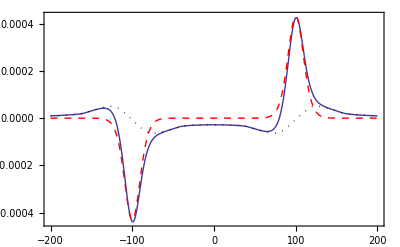

```mathematica
D2symGamma1[eVmev_]:=D2sym[0.05,2,-5,0.1,0.2,50*0.025/300,-0.0097,eVmev];
D2asymGamma1[eVmev_]:=D2asym[0.05,2,-5,0.1,0.2,50*0.025/300,-0.0097,eVmev];
D2Gamma1[eVmev_]:=D2[0.05,2,-5,0.1,0.2,50*0.025/300,-0.0097,eVmev];
Plot[{D2Gamma1[eVmev],D2symGamma1[eVmev],D2asymGamma1[eVmev]},{eVmev,-200,200},PlotStyle->{{Thick},{Thick, Red,Dashed},{Thick,Black,Dotted}},PlotRange->All,Frame->True]
```

Case 2
Gam1 = 0.1, Gam2 = 2 (alpha = Gam2/Gam1 = 20)
e0 = -5
hw = 0.1
M= 0.2
kT= 50*0.025/300
para= -0.0097

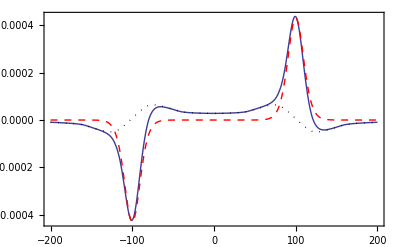

```mathematica
D2symGamma2[eVmev_]:=D2sym[20,0.1,-5,0.1,0.2,50*0.025/300,-0.0097,eVmev];
D2asymGamma2[eVmev_]:=D2asym[20,0.1,-5,0.1,0.2,50*0.025/300,-0.0097,eVmev];
D2Gamma2[eVmev_]:=D2[20,0.1,-5,0.1,0.2,50*0.025/300,-0.0097,eVmev];
Plot[{D2Gamma2[eVmev],D2symGamma2[eVmev],D2asymGamma2[eVmev]},{eVmev,-200,200},PlotStyle->{{Thick},{Thick, Red,Dashed},{Thick,Black,Dotted}},PlotRange->All,Frame->True]
```

IV. Doublet splitting simulation

```mathematica
D2doublet[alpha_,Gam1_,e0_,hw1_,hw2_,M_,kT_,para1_,para2_,eVmev_]:=D2[alpha,Gam1,e0,hw1,M,kT,para1,eVmev]+D2[alpha,Gam1,e0,hw2,M,kT,para2,eVmev];
```

Case of doublet splitting simulation
Gam1 = 2, Gam2 = 0.1, alpha = Gam2/Gam1 = 0.05
e0 = -5
hw1 = 0.1245
hw2 = 0.1
M = 0.2
kT = 38 * 0.025/300
para1 = -0.00
para2 = -0.00

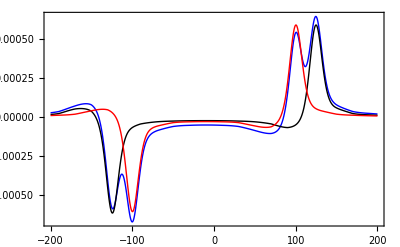

```mathematica
Plot[{D2doublet[0.05,2,-5,0.1,0.1245,0.2,38*0.025/300,-0.00,-0.00,eVmev],D2[0.05,2,-5,0.1245,0.2,38*0.025/300,-0,eVmev],D2[0.05,2,-5,0.1,0.2,38*0.025/300,-0,eVmev]},{eVmev,-200,200},PlotStyle->{{Thick,Blue},{Thick,Black},{Thick,Red}},PlotRange->All,Frame->True]
```